## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`';
Get["MASSef`"];
Get["MASSef`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
rxnName="GAPD";
fitLabel=rxnName;
dataFileName=rxnName;
KeqEquilibrator=0.408;

assumedUncertaintyFraction = 0.05;
removeInputFiles = True;
removeOutputFiles = True;
(* user will need to change this path *)
pathMASSFittingPackage = "/home/mrama/Dropbox/test bla/MASSef/";

mainFolder = "fit_GAPD";
{workingDir, pathData, runFitScriptPath, inputPath, outputPath, bigg2equilibrator}=initializeNotebook[pathMASSFittingPackage, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
enzymeDataPath = FileNameJoin[{pathData, "kinetic_data.csv"}, OperatingSystem->$OperatingSystem];
bufferInfoDataPath = FileNameJoin[{pathData, "buffer_info.csv"}, OperatingSystem->$OperatingSystem];
ionChargeDataPath = FileNameJoin[{pathData, "ion_charge.csv"}, OperatingSystem->$OperatingSystem];

{rxn, mechanism, structure, nActiveSites, nAllostericSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}=getEnzymeData[rxnName, enzymeDataPath, assumedUncertaintyFraction];

bufferInfo = getBufferInfoData[bufferInfoDataPath];
ionCharge = getIonData[ionChargeDataPath];

inhibitorMet={};
affectedMets={};(*There can be multiple metabolites*)
```

## Construct Module and Set Up Comparison Equations

```mathematica
printEnzymeData[rxn, mechanism, structure, nActiveSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; [nad,g3p,pi,13dpg,nadh]

Structure: 4

Active sites: 4

Km Values:

Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
nad | 0.000045 | 0.000041
0.000049 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
g3p | 0.00089 | 0.0008455
0.0009345 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
pi | 0.00053 | 0.00042
0.00064 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
g3p | Null
nad | Null
pi | Null | 268 | 262.
274. | 1/s | 8.9 | 22 | teoa | 0.04 |

Inhibition Values:

Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Parameter_Type | Metabolite | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
Kd | nad | 3.2×10^-7 | 2.5×10^-7
3.9×10^-7 | M | 8.9 | 22 | teoa | 0.04 |

### Construct enzyme module

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi
"[nad,g3p,pi,1,3-diphosphoglycerate,nadh]"

```mathematica
catalyticBranch={"E_GAPD[c] + nad[c] <=> E_GAPD[c]&nad",
				"E_GAPD[c]&nad + g3p[c] <=> E_GAPD[c]&nad&g3p",
				"E_GAPD[c]&nad&g3p + pi[c] <=> E_GAPD[c]&nad&g3p&pi",
				"E_GAPD[c]&nad&g3p&pi <=> E_GAPD[c]&nadh&13dpg",
				"E_GAPD[c]&nadh&13dpg <=> E_GAPD[c]&nadh + 13dpg[c]",
				"E_GAPD[c]&nadh<=> E_GAPD[c] + nadh[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,((GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c)^GAPD2,((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,((GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c)^GAPD4,((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,Overscript[(GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c, GAPD2],((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,Overscript[(GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c, GAPD4],((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

### Setup King-Altmann Equations

```mathematica
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};
```

```mathematica
{haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, eqRateConstSub,
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, {inhibitionList[2]}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  simplifyMaxTime, nActiveSites];
```

creating it

kcat for

kcat rev

km for

km rev

```mathematica
haldaneRatiosList
```

{(k_GAPD1^⟶ k_GAPD2^⟶ k_GAPD3^⟶ k_GAPD4^⟶ k_GAPD5^⟶ k_GAPD6^⟶)/(k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD3^⟵ k_GAPD4^⟵ k_GAPD5^⟵ k_GAPD6^⟵)}

```mathematica
(*{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
rates = getEnzymeRates[enzymeModel];
{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];

(*competitiveRxns={};(*Initialization for later. Do not modify this*)
eqRateConstSub={};(*Initialization for later. Do not modify this*)*)

(*You could modify these, but you shouldn't unless you run into problems*)


simplifyMaxTime=1*^-5;

(*Extract Transition ID from Mass Action Equations and Separate Catalytic and Non-Catalytic Reactions*)
(*The transition indices are extracted based off of the sum of their mass action stoichiometry.Reactions with a sum of zero are assumed to be catalytic.*)

(*Separate Catalytic and Non-Catalytic Reactions*)
{allCatalyticReactions, nonCatalyticReactions}=classifyReactions[enzymeModel];


(*Identify Transition Rate Equations*)
transitionID =getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs=getTransitionRateEqs[transitionID, rates];

unifiedRateConstList=getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions];


(* semi-automated add competitive inhibition steps - none in this enzyme*)
eqRateConstSub={};


(*King-Altman Workaround UsingMathematicaSolve*)
(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)
simplifyMaxTime = 100; (*in seconds*)
absoluteFlux=getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs, simplifyMaxTime, nActiveSites];


(*Equivalent Rate Constant Substitution for Random Ordered Mechanisms*)
(*This should work automatically,a substitution rule list is created with the name:'eqRateConstSub'.It is kind of a greedy section of code,so double check the results to make sure they're accurate*)
eqRateConstSub=getEquivRateConsts[enzymeModel, eqRateConstSub, nonCatalyticReactions];

(*Assemble Kinetic MASS Action Comparision Equations that Match to Km and kcat Data*)
(*Simplify fixes Python evaluation issues dealing with fractional exponents (e.g.'(-1)**(3/5)' returns 1.0)*)
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse}=getRateEqs[absoluteFlux, unifiedRateConstList, eqRateConstSub, reverseZeroSub, forwardZeroSub, volumeSub, metSatForSub, metSatRevSub];

haldaneRatiosList  = Table[
	haldane=haldaneRelation[KeqName,catalyticReactionsSet]/.unifiedRateConstList;
	haldane[[2]],
{catalyticReactionsSet, catalyticReactionsSetsList}];


(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub}=getMetRatesSubs[enzymeModel, haldaneRatiosList,absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse,KeqVal];

(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub}=exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub];*)
```

kcat for

kcat rev

km for

km rev

## Semi-Automated Simulate Data

```mathematica
haldaneRatiosList
```

haldaneRatiosList

```mathematica
haldaneDataList=Table[
	{haldaneRatio, KeqEquilibrator,{0.9*KeqEquilibrator,1.1*KeqEquilibrator}},
{haldaneRatio, haldaneRatiosList}];

customRatiosDataList={{(Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶Subscript[k, GAPD5]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵Subscript[k, GAPD5]^⟵), 4.25*10^2,{0.9*4.25*10^2,1.1*4.25*10^2}}};
```

Table::iterb: Iterator {haldaneRatio,haldaneRatiosList} does not have appropriate bounds.

### Simulate data without uncertainty

```mathematica
Export["GAPDSimulateDataArguments.mx",{enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, eqRateConstSub, customRatiosDataList}, "MX"];
Export["GAPDSimulateDataResults.mx",{allFittingData, dataPath, fileList, fileListSub},"MX"];
```

```mathematica
{allFittingData, dataPath, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, eqRateConstSub, customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

```mathematica
FilePrint@dataPath
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.408
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.408
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.408
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.408
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.408
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.408
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.408
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.408
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.408
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.408
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.408
0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.13680688860321014
0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310194
0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.28474724895080133
0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.386863179846857
0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000002
0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491989
0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909093
0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.090909090909091
0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.1368068886032102
0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131019
0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508017
0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.3868631798468571
0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.5000000000000003
0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.6131368201531434
0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491988
0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868984
0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.86319311139679
0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909092
0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.09090909090909094
0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321008
0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310175
0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508015
0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468569
0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491988
0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.8631931113967899
0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909092
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

### Simulate data with uncertainty

```mathematica
Export["GAPDSimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, KeqName,allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, eqRateConstSub, customRatiosDataList}, "MX"];

Export["GAPDSimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
Get["MASSef`"];
Get["MASSef`"];

nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, KeqName,allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, eqRateConstSub, customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3872599114798666
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3872599114798666
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3872599114798666
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3872599114798666
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3872599114798666
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3872599114798666
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3872599114798666
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3872599114798666
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3872599114798666
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3872599114798666
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3872599114798666
0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.1368068886032101
0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310197
0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.2847472489508014
0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.38686317984685703
0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000001
0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491988
0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909091
0	0.00010091718583050879	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.09090909090909087
0	0.0001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.13680688860321003
0	0.0002534925097937858	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131016
0	0.0004017585531120535	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508014
0	0.0006367443958403206	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.386863179846857
0	0.001009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.4999999999999999
0	0.001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.613136820153143
0	0.0025349250979378583	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491984
0	0.0040175855311205344	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868982
0	0.006367443958403205	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.8631931113967901
0	0.01009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909091
0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.0909090909090909
0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321005
0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310167
0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508014
0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468568
0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491987
0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.86319311139679
0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909091
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
Export["GAPDParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, eqRateConstSub, customRatiosDataList}, "MX"];

Export["GAPDParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
Get["MASSef`"];
Get["MASSef`"];
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",2,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, eqRateConstSub, customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«18 more identical outputs»

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=1;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	1
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateRev_13dpg.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateRev_nadh.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateRev_13dpg.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateRev_nadh.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

### Run Fitting on your Local System

```mathematica
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python","\""<>runFitScriptPath <>"\"", "\""<>psoParameterPath <>"\"", "\""<>lmaParameterPath <>"\"", "\""<>psoTrialSummaryFileName <>"\"","\""<> psoResultsFileName <>"\"", "\""<>lmaResultsFileName <>"\"", ToString @numTrials, "\""<>dataPath <>"\""}, " "];

runBothCmd="cd \""<>inputPath<>"\" && "<>runPythonCmd;
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"]
```

best_fit: 2.91914995435
best_fit: 1.04897924636
best_fit: 1.01249180433
best_fit: 0.938261590057
best_fit: 0.838935927002

### Run Fitting on your Local System with uncertainty or parameter scan

```mathematica
Do[
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python",
						"\""<>runFitScriptPath <>"\"",
						 "\""<>psoParameterPath <>"\"",
						 "\""<>lmaParameterPath <>"\"", 
						"\""<> StringTake[psoTrialSummaryFileName, ;;-5] <>"_"<>ToString[datasetI] <>".txt\"",
						"\""<> StringTake[psoResultsFileName, ;;-5] <>"_"<>ToString[datasetI] <>".txt\"",
						 "\""<>StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt\"", ToString @numTrials, 
						"\""<>dataPathList[[datasetI]] <>"\""}, " "];

runBothCmd="cd \""<>inputPath<>"\" && "<>runPythonCmd;
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"] ,

{datasetI, 1, Length@dataPathList}];
```

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
lmaResultsFileName="lmaResults_GAPD_2017531321_4.txt";
```

```mathematica
splitChar = If[$OperatingSystem == "Windows", "\\", "/"];

resultsFileName = StringSplit[lmaResultsFileName, splitChar][[-1]];
(*fittingData = Import[FileNameJoin[{inputPath, dataFileName<>".dat"}, OperatingSystem->$OperatingSystem]];*)

fittingData=Import[dataPathList[[4]]];
fittingData = fittingData[[2;;,All]];
resultsFile = FileNameJoin[{"raw",resultsFileName}, OperatingSystem->$OperatingSystem];
flagFitType = "abs_ssd";

{flagFitLocal, msgLocal, filteredDataList, bestFitDetails}=getRatesWithSSD[resultsFile, rxnName, fittingData, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, {}, False,fitLabel];
```

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Residual | Residual^2 | Relative error | True value | Predicted Value
 |  |  |  |  | 
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
relRateFor_nad | 0.0740369 | 0.00548146 | 15.6737 | 0.0909091 | 0.0766603
relRateFor_nad | 0.0705865 | 0.00498245 | 15.0011 | 0.136807 | 0.116284
relRateFor_nad | 0.0657327 | 0.00432078 | 14.0458 | 0.20076 | 0.172562
relRateFor_nad | 0.0592748 | 0.0035135 | 12.7581 | 0.284747 | 0.248419
relRateFor_nad | 0.0512914 | 0.0026308 | 11.1395 | 0.386863 | 0.343768
relRateFor_nad | 0.0422715 | 0.00178688 | 9.27468 | 0.5 | 0.453627
relRateFor_nad | 0.0330603 | 0.00109299 | 7.32989 | 0.613137 | 0.568195
relRateFor_nad | 0.0245753 | 0.000603945 | 5.50155 | 0.715253 | 0.675903
relRateFor_nad | 0.0174702 | 0.000305208 | 3.94283 | 0.79924 | 0.767727
relRateFor_nad | 0.0119809 | 0.000143541 | 2.72099 | 0.863193 | 0.839706
relRateFor_nad | 0.0079981 | 0.0000639697 | 1.82478 | 0.909091 | 0.892502
relRateFor_g3p | 0.255805 | 0.0654361 | 44.5125 | 0.0909091 | 0.0504432
relRateFor_g3p | 0.245933 | 0.0604833 | 43.2368 | 0.136807 | 0.0776559
relRateFor_g3p | 0.231794 | 0.0537283 | 41.3583 | 0.20076 | 0.117729
relRateFor_g3p | 0.212496 | 0.0451547 | 38.6939 | 0.284747 | 0.174567
relRateFor_g3p | 0.187817 | 0.0352751 | 35.1092 | 0.386863 | 0.251039
relRateFor_g3p | 0.158729 | 0.0251947 | 30.6141 | 0.5 | 0.34693
relRateFor_g3p | 0.127552 | 0.0162694 | 25.4499 | 0.613137 | 0.457094
relRateFor_g3p | 0.0973507 | 0.00947716 | 20.0811 | 0.715253 | 0.571622
relRateFor_g3p | 0.0708341 | 0.00501748 | 15.0495 | 0.79924 | 0.678958
relRateFor_g3p | 0.049498 | 0.00245005 | 10.7718 | 0.863193 | 0.770211
relRateFor_g3p | 0.0335125 | 0.00112309 | 7.42633 | 0.909091 | 0.841579
relRateFor_pi | 0.183693 | 0.0337429 | 52.6485 | 0.0909091 | 0.138771
relRateFor_pi | 0.172299 | 0.0296871 | 48.696 | 0.136807 | 0.203426
relRateFor_pi | 0.156907 | 0.0246197 | 43.5181 | 0.20076 | 0.288127
relRateFor_pi | 0.137487 | 0.0189027 | 37.242 | 0.284747 | 0.390793
relRateFor_pi | 0.114988 | 0.0132223 | 30.3132 | 0.386863 | 0.504134
relRateFor_pi | 0.0913515 | 0.0083451 | 23.4103 | 0.5 | 0.617052
relRateFor_pi | 0.0689349 | 0.00475203 | 17.202 | 0.613137 | 0.718608
relRateFor_pi | 0.0496499 | 0.00246511 | 12.1114 | 0.715253 | 0.80188
relRateFor_pi | 0.0344062 | 0.00118379 | 8.2446 | 0.79924 | 0.865134
relRateFor_pi | 0.0231473 | 0.000535798 | 5.47446 | 0.863193 | 0.910448
relRateFor_pi | 0.0152432 | 0.000232356 | 3.57221 | 0.909091 | 0.941566
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03

### Simulated Data and Best Fit Data Plot

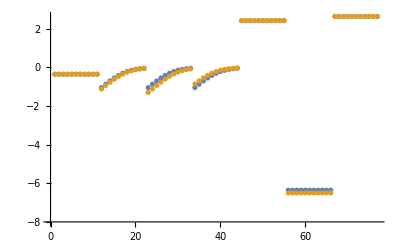

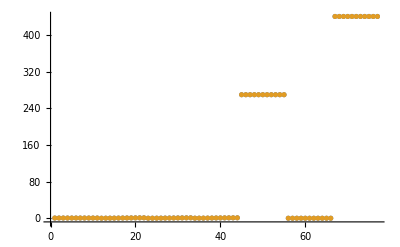

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.0000451708 | 0.37958
0.00089 | 0.000891344 | 0.150985
0.00053 | 0.000530978 | 0.184466

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 1.20456×10^-6

```mathematica
backCalculateRatios[customRatiosList[[1]][[1]], customRatiosList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 0.0000934857

```mathematica
backCalculateRatios[haldaneRatiosList[[1]][[1]], haldaneRatiosList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.40816 | 0.0391769